# Bistable motif: 3 kinase1substrate

## The model

We consider the following reactions:

K+S→KS→K+S_p
K_p+S→K_p S→K_p+S_p
K→K_p
KS←K_p S
E+S→ES→E+S_p
E_p+S→E_p S→E_p+S_p
E→E_p
ES←E_p S
F+S→FS→F+S_p
F_p+S→F_p S→F_p+S_p
F→F_p
FS←F_p S
S_p→S

The species of the system are:

{S,S_p,K,K_p,KS,K_p S,E,E_p,ES,E_p S,F,F_p,FS,F_p S}

In total, there are 19 reations and 14 species.

## Finding the condition of multistationarity

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
ClearAll["Global`*"];
A=Table[0,{19},{14}];
(*For enzyme K*)
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;
A[[2]][[3]]=1;A[[2]][[2]]=1;A[[2]][[5]]=-1;
A[[3]][[1]]=-1;A[[3]][[4]]=-1;A[[3]][[6]]=1;
A[[4]][[4]]=1;A[[4]][[2]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[4]]=1;A[[6]][[5]]=1;A[[6]][[6]]=-1;
(*For enzyme E*)
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[9]]=1;
A[[8]][[7]]=1;A[[8]][[2]]=1;A[[8]][[9]]=-1;
A[[9]][[1]]=-1;A[[9]][[8]]=-1;A[[9]][[10]]=1;
A[[10]][[8]]=1;A[[10]][[2]]=1;A[[10]][[10]]=-1;
A[[11]][[7]]=-1;A[[11]][[8]]=1;A[[12]][[9]]=1;A[[12]][[10]]=-1;
(*For enzyme F*)
A[[13]][[1]]=-1;A[[13]][[11]]=-1;A[[13]][[13]]=1;
A[[14]][[11]]=1;A[[14]][[2]]=1;A[[14]][[13]]=-1;
A[[15]][[1]]=-1;A[[15]][[12]]=-1;A[[15]][[14]]=1;
A[[16]][[12]]=1;A[[16]][[2]]=1;A[[16]][[14]]=-1;
A[[17]][[11]]=-1;A[[17]][[12]]=1;A[[18]][[13]]=1;A[[18]][[14]]=-1;
(*Autophosphorylation*)
A[[19]][[2]]=-1;A[[19]][[1]]=1;
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,-1,0,0,0,-1,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 4]×Subscript[x, 6],Subscript[k, 5]×Subscript[x, 3],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 7]×Subscript[x, 1],Subscript[k, 8]×Subscript[x, 9],Subscript[k, 9]×Subscript[x, 8]*Subscript[x, 1],Subscript[k, 10]*Subscript[x, 10],Subscript[k, 11]*Subscript[x, 7],Subscript[k, 12]×Subscript[x, 10],Subscript[k, 13]×Subscript[x, 11]×Subscript[x, 1],Subscript[k, 14]×Subscript[x, 13],Subscript[k, 15]×Subscript[x, 12]*Subscript[x, 1],Subscript[k, 16]*Subscript[x, 14],Subscript[k, 17]*Subscript[x, 11],Subscript[k, 18]×Subscript[x, 14],Subscript[k, 19]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_5,k_3 x_1 x_4,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_9,k_9 x_1 x_8,k_10 x_10,k_11 x_7,k_12 x_10,k_13 x_1 x_11,k_14 x_13,k_15 x_1 x_12,k_16 x_14,k_17 x_11,k_18 x_14,k_19 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_19 x_2-k_1 x_1 x_3-k_3 x_1 x_4-k_7 x_1 x_7-k_9 x_1 x_8-k_13 x_1 x_11-k_15 x_1 x_12,-k_19 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10+k_14 x_13+k_16 x_14,-k_5 x_3-k_1 x_1 x_3+k_2 x_5,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,-k_11 x_7-k_7 x_1 x_7+k_8 x_9,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,k_9 x_1 x_8-k_10 x_10-k_12 x_10,-k_17 x_11-k_13 x_1 x_11+k_14 x_13,k_17 x_11-k_15 x_1 x_12+k_16 x_14,k_13 x_1 x_11-k_14 x_13+k_18 x_14,k_15 x_1 x_12-k_16 x_14-k_18 x_14}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,0,1,1,0,0,1,1,0,0,1,1},{0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]+Subscript[x, 13]+Subscript[x, 14]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2],Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 3],Subscript[x, 11]+Subscript[x, 12]+Subscript[x, 13]+Subscript[x, 14]-Subscript[T, 4]};
```

```mathematica
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],ssEqns[[8]],ssEqns[[9]],cons[[1]],cons[[2]],cons[[3]]}
```

{-k_19 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10+k_14 x_13+k_16 x_14,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,-T_1+x_1+x_2+x_5+x_6+x_9+x_10+x_13+x_14,-T_2+x_3+x_4+x_5+x_6,-T_3+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[{ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{{x_3→(k_2 k_3 k_6 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_4→(k_2 k_5 (k_4+k_6) T_2)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_5→(k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_6→(k_2 k_3 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)}}

```mathematica
sol2=Solve[{ssEqns[[8]],ssEqns[[9]],ssEqns[[10]],cons[[3]]}==0,{Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_7→(k_8 k_9 k_12 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_8→(k_8 k_11 (k_10+k_12) T_3)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_9→(k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_10→(k_8 k_9 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)}}

```mathematica
sol3=Solve[{ssEqns[[12]],ssEqns[[13]],ssEqns[[14]],cons[[4]]}==0,{Subscript[x, 11],Subscript[x, 12],Subscript[x, 13],Subscript[x, 14]}]
```

{{x_11→(k_14 k_15 k_18 T_4 x_1)/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2),x_12→(k_14 k_17 (k_16+k_18) T_4)/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2),x_13→(k_15 T_4 (k_17 k_18 x_1+k_13 k_18 x_1^2))/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2),x_14→(k_14 k_15 k_17 T_4 x_1)/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2)}}

```mathematica
sol4=Subscript[x, 2]/.Solve[{ssEqns[[2]]==0},{Subscript[x, 2]}]
```

{(k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10+k_14 x_13+k_16 x_14)/k_19}

```mathematica
sol5=Solve[{Subscript[x, 2]==sol4[[1]]}/.Join[sol1[[1]],sol2[[1]],sol3[[1]]],{Subscript[x, 2]}]
```

{{x_2→1/k_19((k_2 k_3 k_4 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_2 k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_8 k_9 k_10 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_8 k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_14 k_15 k_16 k_17 T_4 x_1)/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2)+(k_14 k_15 T_4 (k_17 k_18 x_1+k_13 k_18 x_1^2))/(k_14 k_16 k_17+k_14 k_17 k_18+k_14 k_15 k_17 x_1+k_14 k_15 k_18 x_1+k_15 k_17 k_18 x_1+k_13 k_15 k_18 x_1^2))}}

```mathematica
term=FullSimplify[cons[[1]]/.Join[sol1[[1]],sol2[[1]],sol3[[1]],sol5[[1]]]]
```

-T_1+((k_2+k_19) T_2+(k_14+k_19) T_4)/k_19+x_1+(k_2 T_2 (-k_5 (k_4+k_6) (k_2+k_19)-k_3 (-k_4 k_5+k_2 (k_5+k_6)+k_6 k_19) x_1))/(k_19 (k_3 k_6 x_1 (k_5+k_1 x_1)+k_2 (k_5 (k_4+k_6)+k_3 (k_5+k_6) x_1)))+(k_9 T_3 x_1 (k_11 (k_12 k_19+k_8 (k_10+k_12+k_19))+k_7 k_12 (k_8+k_19) x_1))/(k_19 (k_9 k_12 x_1 (k_11+k_7 x_1)+k_8 (k_11 (k_10+k_12)+k_9 (k_11+k_12) x_1)))+(k_14 T_4 (-k_17 (k_16+k_18) (k_14+k_19)-k_15 (-k_16 k_17+k_14 (k_17+k_18)+k_18 k_19) x_1))/(k_19 (k_15 k_18 x_1 (k_17+k_13 x_1)+k_14 (k_17 (k_16+k_18)+k_15 (k_17+k_18) x_1)))

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

20+(k_1 k_3 k_6 k_7 k_9 k_12 k_14 k_15 k_17 k_19+k_1 k_3 k_6 k_8 k_9 k_11 k_13 k_15 k_18 k_19+k_2 k_3 k_5 k_7 k_9 k_12 k_13 k_15 k_18 k_19+k_2 k_3 k_6 k_7 k_9 k_12 k_13 k_15 k_18 k_19+10+k_1 k_3 k_6 k_7 k_9 k_12 k_13 k_15 k_18 k_19 T_3+k_1 k_3 k_6 k_7 k_9 k_12 k_13 k_14 k_15 k_18 T_4+k_1 k_3 k_6 k_7 k_9 k_12 k_13 k_15 k_18 k_19 T_4) x_1^6+k_1 k_3 k_6 k_7 k_9 k_12 k_13 k_15 k_18 k_19 x_1^7
 |  |  |  |

## Sampling and bifurcation analysis

```mathematica
term=-Subscript[T, 1]+((Subscript[k, 2]+Subscript[k, 19]) Subscript[T, 2]+(Subscript[k, 14]+Subscript[k, 19]) Subscript[T, 4])/Subscript[k, 19]+Subscript[x, 1]+(Subscript[k, 2] Subscript[T, 2] (-Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6]) (Subscript[k, 2]+Subscript[k, 19])-Subscript[k, 3] (-Subscript[k, 4] Subscript[k, 5]+Subscript[k, 2] (Subscript[k, 5]+Subscript[k, 6])+Subscript[k, 6] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 3] Subscript[k, 6] Subscript[x, 1] (Subscript[k, 5]+Subscript[k, 1] Subscript[x, 1])+Subscript[k, 2] (Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6])+Subscript[k, 3] (Subscript[k, 5]+Subscript[k, 6]) Subscript[x, 1])))+(Subscript[k, 9] Subscript[T, 3] Subscript[x, 1] (Subscript[k, 11] (Subscript[k, 12] Subscript[k, 19]+Subscript[k, 8] (Subscript[k, 10]+Subscript[k, 12]+Subscript[k, 19]))+Subscript[k, 7] Subscript[k, 12] (Subscript[k, 8]+Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 9] Subscript[k, 12] Subscript[x, 1] (Subscript[k, 11]+Subscript[k, 7] Subscript[x, 1])+Subscript[k, 8] (Subscript[k, 11] (Subscript[k, 10]+Subscript[k, 12])+Subscript[k, 9] (Subscript[k, 11]+Subscript[k, 12]) Subscript[x, 1])))+(Subscript[k, 14] Subscript[T, 4] (-Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18]) (Subscript[k, 14]+Subscript[k, 19])-Subscript[k, 15] (-Subscript[k, 16] Subscript[k, 17]+Subscript[k, 14] (Subscript[k, 17]+Subscript[k, 18])+Subscript[k, 18] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 15] Subscript[k, 18] Subscript[x, 1] (Subscript[k, 17]+Subscript[k, 13] Subscript[x, 1])+Subscript[k, 14] (Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18])+Subscript[k, 15] (Subscript[k, 17]+Subscript[k, 18]) Subscript[x, 1])));
```

```mathematica
pol=Collect[Numerator[Together[term]],Subscript[x, 1]];
```

### Sampling

```mathematica
SeedRandom[];
ss7ParSets={};
ss7PolSets={};
ss7SolSets={};
minPar=Log[0.000001];maxPar=Log[1000000.];
minTot=Log[0.0001];maxTot=Log[10000.];
biCount=0;
(*multiCount=0;*)
(*termCount=0;*)
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{minPar,maxPar},19]];
tots=Exp[RandomReal[{minTot,maxTot},4]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[k, 14]->pars[[14]],Subscript[k, 15]->pars[[15]],Subscript[k, 16]->pars[[16]],Subscript[k, 17]->pars[[17]],Subscript[k, 18]->pars[[18]],Subscript[k, 19]->pars[[19]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]],Subscript[T, 4]->tots[[4]]};
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
If[Length[Flatten[solution]]==7,{
AppendTo[ss7ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss7PolSets,pol/.subs];
AppendTo[ss7SolSets,Flatten[solution]];}
];
},{i,5000000}];
]
```

```mathematica
Length[ss7ParSets]
```

0

## Using repetitive parameters from 1 kinase 1 substrate system

```mathematica
ClearAll["Global`*"];
```

```mathematica
ss5Par3={5.879137085516735,0.0033751979024755916,2.107719796978838,500.69023689470674,0.037972916416413455,48.025982227857675,67.40947817881231,0.004277486460006026,0.16410793866624665,30.195763275878235,0.4278526927277934,0.002727157259805876,0.0015127395140503617,829.7331212580159,110.97744997193716,25.07248294701992};
```

```mathematica
term=-Subscript[T, 1]+((Subscript[k, 2]+Subscript[k, 19]) Subscript[T, 2]+(Subscript[k, 14]+Subscript[k, 19]) Subscript[T, 4])/Subscript[k, 19]+Subscript[x, 1]+(Subscript[k, 2] Subscript[T, 2] (-Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6]) (Subscript[k, 2]+Subscript[k, 19])-Subscript[k, 3] (-Subscript[k, 4] Subscript[k, 5]+Subscript[k, 2] (Subscript[k, 5]+Subscript[k, 6])+Subscript[k, 6] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 3] Subscript[k, 6] Subscript[x, 1] (Subscript[k, 5]+Subscript[k, 1] Subscript[x, 1])+Subscript[k, 2] (Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6])+Subscript[k, 3] (Subscript[k, 5]+Subscript[k, 6]) Subscript[x, 1])))+(Subscript[k, 9] Subscript[T, 3] Subscript[x, 1] (Subscript[k, 11] (Subscript[k, 12] Subscript[k, 19]+Subscript[k, 8] (Subscript[k, 10]+Subscript[k, 12]+Subscript[k, 19]))+Subscript[k, 7] Subscript[k, 12] (Subscript[k, 8]+Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 9] Subscript[k, 12] Subscript[x, 1] (Subscript[k, 11]+Subscript[k, 7] Subscript[x, 1])+Subscript[k, 8] (Subscript[k, 11] (Subscript[k, 10]+Subscript[k, 12])+Subscript[k, 9] (Subscript[k, 11]+Subscript[k, 12]) Subscript[x, 1])))+(Subscript[k, 14] Subscript[T, 4] (-Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18]) (Subscript[k, 14]+Subscript[k, 19])-Subscript[k, 15] (-Subscript[k, 16] Subscript[k, 17]+Subscript[k, 14] (Subscript[k, 17]+Subscript[k, 18])+Subscript[k, 18] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 15] Subscript[k, 18] Subscript[x, 1] (Subscript[k, 17]+Subscript[k, 13] Subscript[x, 1])+Subscript[k, 14] (Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18])+Subscript[k, 15] (Subscript[k, 17]+Subscript[k, 18]) Subscript[x, 1])));
pol=Collect[Numerator[Together[term]],Subscript[x, 1]];
```

```mathematica
SeedRandom[];
ss7ParSets={};
ss7PolSets={};
ss7SolSets={};
minPar=Log[0.000001];maxPar=Log[1000000.];
minTot=Log[0.0001];maxTot=Log[10000.];
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{minPar,maxPar},6]];
tots=Exp[RandomReal[{minTot,maxTot},1]];
subs={Subscript[k, 1]->ss5Par3[[1]],Subscript[k, 2]->ss5Par3[[2]],Subscript[k, 3]->ss5Par3[[3]],Subscript[k, 4]->ss5Par3[[4]],Subscript[k, 5]->ss5Par3[[5]],Subscript[k, 6]->ss5Par3[[6]],Subscript[k, 7]->ss5Par3[[7]],Subscript[k, 8]->ss5Par3[[8]],Subscript[k, 9]->ss5Par3[[9]],Subscript[k, 10]->ss5Par3[[10]],Subscript[k, 11]->ss5Par3[[11]],Subscript[k, 12]->ss5Par3[[12]],Subscript[k, 13]->pars[[1]],Subscript[k, 14]->pars[[2]],Subscript[k, 15]->pars[[3]],Subscript[k, 16]->pars[[4]],Subscript[k, 17]->pars[[5]],Subscript[k, 18]->pars[[6]],Subscript[k, 19]->ss5Par3[[13]],Subscript[T, 1]->ss5Par3[[14]],Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->ss5Par3[[16]],Subscript[T, 4]->tots[[1]]};
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
If[Length[Flatten[solution]]==7,{
AppendTo[ss7ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss7PolSets,pol/.subs];
AppendTo[ss7SolSets,Flatten[solution]];}
];
},{i,1000000}];
]
```

```mathematica
Length[ss7ParSets]
```

89

```mathematica
InputForm[ss7ParSets]
```

{{438.4624202381857, 0.00006927317341952479, 682370.5555922479, 81.12581861452854, 0.008836693943023586, 
 0.0018454210049659468, 4.065210100758104}, {25528.145726695868, 0.00039543772295879244, 612075.7087721903, 
 1087.3115486818779, 0.000010695908903036156, 0.000015579733574117894, 4.325814423614453}, {59022.5132582486, 
 6.152580130730356*^-6, 278013.94086279446, 43193.66972720107, 0.08207732700916412, 0.0030729312937503093, 
 6.9193578387957935}, {169.7510372744657, 0.0000677838063854684, 957134.64599272, 431.7402088140664, 
 0.010328705244064911, 0.8982974713701483, 45.52062157587965}, {0.9127765054351228, 6.943495089603213*^-6, 
 95841.86256690184, 271.96426095608234, 0.000045759256888719464, 0.00106651630205654, 1.7912671838841963}, 
 {59460.2227461117, 0.00011524516567484025, 12269.939369216087, 16758.83907104939, 0.00030617902787272584, 
 0.08974349560741363, 66.01936397272112}, {19.581072356799286, 0.00023636595081656168, 4222.158734836759, 
 2674.8419684823625, 0.00028885975550980666, 0.3200423067085498, 51.58962497826906}, {268890.3532950944, 
 0.0005173036838390276, 1179.6653641392497, 1.7740585275315772, 0.18146772628136848, 0.000020082759047984177, 
 36.48700623412346}, {10110.702637622571, 0.000255120246130665, 10521.763498964667, 1.4597816086258055, 
 0.4791149066825248, 0.001259128025730661, 45.47448309877031}, {4680.389216564439, 0.00007306930245622418, 
 9857.206314756904, 119.41873693694869, 0.13108944594684319, 0.005395695105994621, 26.785279877176187}, 
 {703.4038914040447, 0.001403070846501467, 18099.168406378783, 2149.020730105172, 0.00004869693316150681, 
 0.007695486320426195, 35.958489089862226}, {295829.15995323844, 0.19037846532507266, 955977.5221244496, 
 342.0918296183876, 0.01227177838644085, 0.01082373245002661, 0.37640158041863453}, {1005.9160180682012, 
 0.00005296371706045712, 11923.683354918508, 94.03222285064473, 0.1369846625547226, 0.0011806582816618622, 
 1.3885012485795873}, {5222.109915379781, 0.00001969142479910218, 203939.388827377, 902.510442229509, 
 0.0021810393200109874, 0.0002900310802304382, 1.3759075021562894}, {1.4751927993628144, 0.000026302288526544992, 
 136889.06169713437, 454468.9830888848, 0.0005920687244583645, 83.12661310373942, 12.647022847984116}, 
 {551425.5264939986, 0.003409755834501948, 54828.9717661581, 19.754343649345056, 1.1431229427709086, 
 0.0014880890953713616, 2.1636722108059963}, {875776.4773157915, 0.009294131823389498, 748818.1414184236, 
 93899.48250825638, 69.49185899149022, 28.5146524339446, 0.1827270670205207}, {26506.349257565296, 
 0.00024318788895003063, 103337.35605465666, 85234.5884165685, 0.0020912818459703085, 0.05423312305195864, 
 13.47533475005443}, {6.420605447389798, 0.0000875028249875676, 150370.0939241111, 3.5736194232355687, 
 0.0013146697436697318, 0.00014928108745975946, 3.278442762175651}, {15373.459246774186, 0.003930181658566736, 
 231427.71168537255, 913.0707136084045, 0.0007929218756782042, 0.001446367189114892, 1.05034774382593}, 
 {43.138090352133574, 2.8062695660602444*^-6, 35789.04368211806, 210598.7983261009, 0.010663907193840779, 
 2.1080969868687585, 17.919688824334056}, {88130.56041002827, 0.0009434792773420769, 757171.9092092989, 
 33.975561758727004, 0.00001736623830334432, 7.692101037228185*^-6, 7.7698977250674455}, {855875.6224589406, 
 8.556628830735924*^-6, 68509.50786265892, 118300.72923558875, 0.02432280108080108, 0.022058268249935144, 
 45.28291348838665}, {957045.8863247541, 0.0001539473237156179, 10062.503159307316, 14.11710007018987, 
 502.0855778696885, 0.0052643499003538295, 9.812168065268455}, {288.37360565279795, 0.0023851843245724096, 
 3400.957240786585, 129046.058955048, 0.00010045328513175407, 0.5136272036055192, 6.13698065893816}, {5384.500459209863, 
 0.0004517213623830219, 10712.031201993837, 0.08331307490422832, 0.027263696835819896, 1.3728067311972816*^-6, 
 17.710637737101628}, {41344.10420881141, 0.005104696086675666, 84061.12522837239, 65240.42171890771, 
 0.00027128092653528376, 0.0006578669805660545, 0.4062725697702217}, {2360.7867182280966, 0.00035643770523279586, 
 393333.534539692, 349.816073734204, 0.0031767653717018076, 0.00009353500449117122, 0.2660646614165446}, 
 {333.7186100121194, 0.00002989556043609713, 336876.455908679, 0.1479041164749672, 0.006929091103257922, 
 1.8329297177140799*^-6, 25.19377866925571}, {190.76273368277276, 3.123049378769653*^-6, 69840.86716914122, 
 3.64030005313234, 0.0005987754921831505, 8.845062690411633*^-6, 11.283553915687591}, {657422.6615677169, 
 0.0426660364559853, 114200.37252089984, 52.34730983533573, 0.0206054110898313, 0.00012330410961577481, 
 0.4624537291961194}, {449730.992144817, 2.0941162529705266*^-6, 1584.4216829498607, 15042.416102279953, 
 11.474629805235145, 0.059158529660014565, 56.08515369500811}, {2923.6966960458703, 4.564232219238518*^-6, 
 9138.917132824958, 677114.6955730149, 0.004143439574766088, 0.0008220371336867273, 0.3527379495731758}, 
 {20864.077739721164, 7.182607920100571*^-6, 277849.82557581295, 1596.5430962519313, 0.945831044533587, 
 0.0007713807730950465, 0.5512128291464736}, {764.0809032061569, 0.03767812985543545, 525808.233395572, 
 1248.4614481181864, 0.21610020887504774, 0.17970594544234175, 0.021422847783932858}, {555.3499815670607, 
 6.548557663770736*^-6, 447975.28369333956, 251798.86739877966, 0.002856659377606248, 0.006919039951110949, 
 1.376061305013854}, {78.61843406063048, 0.0001739046371355078, 663906.8500506605, 147.4972729035496, 
 0.0022385259773149008, 0.04352481603651413, 42.09638606697228}, {334230.4168063525, 6.946240718619806*^-6, 
 374585.81944307935, 1029.443645139956, 2.8502283546829297, 0.009613588713641987, 22.12858693865944}, 
 {78.57497769974495, 0.00031491283584752643, 17398.481814762185, 18.092646992639686, 0.00003546449321977316, 
 0.0001012280048665235, 31.971121252704833}, {10943.9255778019, 0.0007642407232020689, 292058.4888991202, 
 25472.7986518553, 0.00011927569871631332, 5.003604786008171*^-6, 0.031999258406948665}, {149576.9266144932, 
 0.10557482155246856, 526973.5982716029, 495.7311971376406, 0.5774711114366087, 0.11147987889578012, 
 0.7770318011889645}, {40079.23913337914, 0.020627181909634456, 912016.856832085, 230421.5174145703, 
 0.16438627106891024, 56.31169908528937, 0.2915972013174511}, {1732.6404205282042, 0.0007007840320199179, 
 264137.53772181127, 43.28927690875235, 0.00039203019440118306, 0.0006500294623311604, 4.1457123625066785}, 
 {24532.38290143752, 0.00028872936337264626, 511467.6838660997, 54499.29030290948, 41.23561231425858, 2.836275179479895, 
 0.28522330469920804}, {2.795664429677875, 0.0001504795478333183, 421.6135419649755, 16368.645234249827, 
 9.65306397346988*^-6, 0.057310374196901596, 12.364141884621615}, {2447.1563575936507, 0.000047933411989914254, 
 160054.5260360948, 44651.52354067939, 0.006327838179331247, 0.03760417179726255, 12.318530539233018}, 
 {100.97758526237094, 0.00037828404721787756, 66952.89978154853, 0.023980394936556265, 0.00011454884118027989, 
 2.932855581207716*^-6, 59.284552714658524}, {107.7654961847041, 0.00006613765627804675, 3513.747779851222, 
 13.6186038152632, 0.00008052631024053622, 6.7850765423373015*^-6, 4.455501546506547}, {2177.749806521256, 
 0.00007448198054990273, 873577.1058721056, 0.36327530499715416, 0.000611140153884628, 1.3784205420697186*^-6, 
 69.31383225400342}, {1798.307043461709, 0.00038850917942383873, 11389.594936953587, 286985.1490092135, 
 0.0006387030055360039, 0.07896773016627034, 1.7027012499377832}, {507942.6497118183, 0.0005640234025500595, 
 27106.490454984163, 42.425089615348526, 0.0025934310065977646, 2.145151913747703*^-6, 8.08643726773106}, 
 {52.8034071413945, 0.0013419544214671314, 412999.09323230933, 0.8280429227794783, 0.000365489464365226, 
 0.00006811334577097136, 11.243410867286753}, {0.788586592009087, 5.137623575771693*^-6, 514819.59701821726, 
 17169.4935834615, 7.214558722023361*^-6, 0.09874435128331599, 7.048037482604756}, {186458.60267736964, 
 8.464687634556*^-6, 843648.0728853297, 19.055795597717946, 0.0015105945184471317, 6.14838725113476*^-6, 
 25.10909509065829}, {99103.67546781607, 0.00737979083179146, 233720.89793971117, 10.875255172222909, 
 0.0013328829966896363, 0.000850796716764036, 7.236369051548144}, {20961.425945307114, 0.000031356653774269675, 
 577617.612055038, 7659.048194742134, 0.00005532754580148834, 0.0004531604227913072, 26.68014761191401}, 
 {8964.42625468008, 0.0001808417872017248, 3091.255564106648, 14.502696366916414, 0.003791054829512152, 
 1.4769180014388607*^-6, 2.512246614015887}, {16209.632683084898, 0.0009672923184102236, 708791.1351198754, 
 2067.249488910578, 0.000037028864232944024, 1.1394502485683225*^-6, 0.13561282908913988}, {2691.7765985909173, 
 0.007990049147798453, 100333.17466159572, 291.67770235630434, 0.000023959572054642428, 0.0010391620985592605, 
 8.92892443154594}, {49196.73407488221, 0.0013102475901054854, 31401.215613946595, 3344.5262156504837, 
 0.00007304830219126472, 6.480206585091935*^-6, 0.5075520906826172}, {0.04009789081948141, 2.831617150570816*^-6, 
 59253.49244730006, 112022.26088749556, 7.686649647070814*^-6, 0.18821071683341414, 3.9214146599575503}, 
 {46496.23473168548, 0.000928780553353209, 552377.9836799351, 545.8651526845995, 0.0020547946043780593, 
 3.3945510547138846*^-6, 0.09283778236353173}, {755699.5533531265, 0.00002961651041895735, 170680.86428084268, 
 154918.86756530064, 0.06200546142066733, 16.937075988340837, 45.021014045610904}, {4964.294787037715, 
 0.0011853086049893817, 744637.4148663983, 500545.1820726385, 0.00007538442553490359, 0.28766627269784273, 
 23.5927150409878}, {512.6432501012079, 0.000024372166578362388, 35636.157858320024, 382030.2951578222, 
 0.002050764722065817, 0.0758564662514909, 0.8837064934213088}, {380.7795082814995, 7.23559601227835*^-6, 
 252755.45415904457, 216557.59399856048, 0.0005615807869665012, 0.00025233348405054415, 0.060251462922645174}, 
 {80457.33476986899, 0.00770415903037973, 169834.07405770782, 9441.906747205367, 3.1392309339155903*^-6, 
 6.180045739133998*^-6, 0.8405205906429579}, {269.5816997308942, 0.000012788818669975515, 199764.25437807475, 
 7.2426715014088066, 0.00946947107351635, 0.00003297005170747795, 1.781923276750838}, {31916.173856522037, 
 2.3122268374987634*^-6, 140340.0078155894, 53859.322050369636, 0.0002934539773201344, 0.0008774779226517668, 
 27.82684548418803}, {382.17543926339437, 3.8795557110976824*^-6, 316853.50834214065, 921401.1447558469, 
 6.744149364603664*^-6, 0.0028132313971029224, 2.52488375058828}, {9739.130073333157, 0.027597179004961933, 
 116354.85753377913, 29042.18444780542, 0.8599424334489718, 212.66553935775175, 2.2387683948549872}, 
 {107.45122437342006, 7.108044181612537*^-6, 147467.85932554808, 14921.190909847795, 0.000014292567551650223, 
 0.0001845791693584908, 6.979768522780166}, {3.401563987279536, 7.692124093019525*^-6, 369314.09321781143, 
 50906.9159881081, 4.787675755645398*^-6, 0.014445032451350778, 4.191572706979028}, {571147.2314818653, 
 0.000016109502199317702, 188452.84222160367, 16.868447157933247, 47.31446387436501, 5.605784637324168*^-6, 
 0.4307642744053164}, {158671.9104405897, 0.0005832855427009986, 32531.584495637988, 252207.30194835702, 
 0.20656226425168692, 94.59928619720473, 10.552111744300356}, {150586.9099465044, 0.00009681701634920352, 
 746717.5898677321, 1059.4655252190928, 0.04383427897018747, 0.0011763894837454032, 37.53610852570354}, 
 {1038.696245910281, 0.0011128895317438809, 72767.26813747958, 224.5113770824961, 1.214505631980333*^-6, 
 0.00011210295557531124, 38.25980691687738}, {103.94556616644019, 0.006391433511193063, 7309.7124409007265, 
 1.4645458718331763, 0.00004610266644573069, 4.948825089678451*^-6, 2.116650433138044}, {4807.514214372535, 
 0.0010536115033734834, 3031.4810441830687, 49974.706881499784, 0.0005460723636621066, 0.481240781182499, 
 24.218899181714097}, {489939.81344327616, 0.0012415380480372325, 16381.123770636967, 9466.609213330912, 
 53.583156087289964, 5.158098573478137, 4.377024930211814}, {124633.87609415219, 0.00010941510677605219, 
 3229.9941748445776, 137926.09327066215, 4.857156785918753, 27.763638167481325, 19.57091059154901}, {164779.9415544647, 
 0.00024887931345694435, 108502.01479709806, 14.849976125450645, 0.02892851401150538, 0.00019170836051545775, 
 17.994032554288257}, {13655.220038315882, 0.029102065343765558, 769610.0850808327, 100.062118926731, 
 0.0002323424599873748, 0.000014037937254156027, 0.21038656427485583}, {294665.81509828917, 0.0006551019248697201, 
 15245.622542560699, 71456.4566926375, 0.04226748007737955, 1.4459383946215383, 51.508579826812976}, 
 {208.11835641742752, 0.00032656568389951424, 25085.059773205852, 3.750177028791144, 0.0002103015717427262, 
 0.0001649731983196191, 23.160205145525175}, {4405.586574454167, 0.000024469060670662744, 58979.87968676846, 
 192.02968593657116, 0.00206845309435574, 0.002103074927539725, 24.191415114517675}, {7307.065738576921, 
 0.0039161514165217525, 569681.4754156915, 51.64944506868827, 0.011085708853707675, 0.00004892891512515762, 
 0.2624162425775333}, {949527.5785053681, 0.0017573704477132463, 561804.8145881261, 813852.1162896081, 
 0.016510041377453395, 60.41601050708182, 7.111525527912483}, {817692.0081762813, 0.000020225915937038516, 
 5308.999420320186, 1572.2319295936677, 5.023566246221323, 0.013989657795916712, 55.40844997964766}}

```mathematica
goodSols={5,8,13,16,17,24,25,26,27,28,31,32,33,34,35,40,44,45,48,50,57,58,60,62,65,66,74,78,79,80,81};
```

```mathematica
ss7Pars=ss7ParSets[[goodSols]]
```

{{0.912777,6.9435×10^-6,95841.9,271.964,0.0000457593,0.00106652,1.79127},{268890.,0.000517304,1179.67,1.77406,0.181468,0.0000200828,36.487},{1005.92,0.0000529637,11923.7,94.0322,0.136985,0.00118066,1.3885},{551426.,0.00340976,54829.,19.7543,1.14312,0.00148809,2.16367},{875776.,0.00929413,748818.,93899.5,69.4919,28.5147,0.182727},{957046.,0.000153947,10062.5,14.1171,502.086,0.00526435,9.81217},{288.374,0.00238518,3400.96,129046.,0.000100453,0.513627,6.13698},{5384.5,0.000451721,10712.,0.0833131,0.0272637,1.37281×10^-6,17.7106},{41344.1,0.0051047,84061.1,65240.4,0.000271281,0.000657867,0.406273},{2360.79,0.000356438,393334.,349.816,0.00317677,0.000093535,0.266065},{657423.,0.042666,114200.,52.3473,0.0206054,0.000123304,0.462454},{449731.,2.09412×10^-6,1584.42,15042.4,11.4746,0.0591585,56.0852},{2923.7,4.56423×10^-6,9138.92,677115.,0.00414344,0.000822037,0.352738},{20864.1,7.18261×10^-6,277850.,1596.54,0.945831,0.000771381,0.551213},{764.081,0.0376781,525808.,1248.46,0.2161,0.179706,0.0214228},{10943.9,0.000764241,292058.,25472.8,0.000119276,5.0036×10^-6,0.0319993},{24532.4,0.000288729,511468.,54499.3,41.2356,2.83628,0.285223},{2.79566,0.00015048,421.614,16368.6,9.65306×10^-6,0.0573104,12.3641},{107.765,0.0000661377,3513.75,13.6186,0.0000805263,6.78508×10^-6,4.4555},{1798.31,0.000388509,11389.6,286985.,0.000638703,0.0789677,1.7027},{8964.43,0.000180842,3091.26,14.5027,0.00379105,1.47692×10^-6,2.51225},{16209.6,0.000967292,708791.,2067.25,0.0000370289,1.13945×10^-6,0.135613},{49196.7,0.00131025,31401.2,3344.53,0.0000730483,6.48021×10^-6,0.507552},{46496.2,0.000928781,552378.,545.865,0.00205479,3.39455×10^-6,0.0928378},{512.643,0.0000243722,35636.2,382030.,0.00205076,0.0758565,0.883706},{380.78,7.2356×10^-6,252755.,216558.,0.000561581,0.000252333,0.0602515},{571147.,0.0000161095,188453.,16.8684,47.3145,5.60578×10^-6,0.430764},{103.946,0.00639143,7309.71,1.46455,0.0000461027,4.94883×10^-6,2.11665},{4807.51,0.00105361,3031.48,49974.7,0.000546072,0.481241,24.2189},{489940.,0.00124154,16381.1,9466.61,53.5832,5.1581,4.37702},{124634.,0.000109415,3229.99,137926.,4.85716,27.7636,19.5709}}

```mathematica
ss7Sols=ss7SolSets[[goodSols]]
```

{{0.0000181302,0.0000525252,0.010438,0.0260613,0.130288,13.7116,359.475},{0.0000305435,0.00121046,0.00587222,0.0453537,0.0964548,15.945,310.095},{0.000125394,0.000446219,0.00831926,0.0293073,0.128686,13.6981,359.851},{0.0000119263,0.000149715,0.00997777,0.027499,0.127268,13.9279,354.019},{0.0000123435,0.00028403,0.00944822,0.0275041,0.129765,13.6921,359.988},{0.0000187567,0.00246163,0.00379821,0.0375636,0.119008,14.0915,350.087},{0.0000637751,0.00133311,0.00631952,0.0350108,0.118785,14.3078,344.87},{0.0000434869,0.000555273,0.00418961,0.0424164,0.109861,14.6354,337.359},{0.0000378023,0.00143708,0.00652863,0.0319974,0.126871,13.713,359.496},{0.0000125991,0.00039358,0.00936977,0.027473,0.130209,13.6528,361.004},{0.0000291037,0.000181631,0.00946003,0.0293265,0.123436,14.2043,347.28},{0.0000150148,0.000726418,0.006663,0.0463422,0.0924587,16.3519,302.492},{0.000506177,0.00210567,0.00464291,0.0340451,0.126091,13.6565,360.975},{0.0000100747,0.000256528,0.00973056,0.0269595,0.130381,13.6616,360.77},{0.000193215,0.00104803,0.00610551,0.0327101,0.12688,13.664,360.766},{0.000151052,0.00131708,0.00657253,0.0316509,0.127839,13.6432,361.294},{0.0000441312,0.000791275,0.00416223,0.0369339,0.123751,13.6574,360.988},{0.000291913,0.00227427,0.00440419,0.0370606,0.118254,14.2114,347.185},{0.00012258,0.000250213,0.00928425,0.0282383,0.127911,13.8289,356.508},{0.0000712066,0.000732071,0.00807358,0.0297521,0.128126,13.7268,359.119},{0.00018347,0.00251184,0.00444983,0.0346311,0.124624,13.7562,358.418},{0.0000135056,0.000461365,0.00914976,0.027794,0.130081,13.6486,361.114},{0.00010265,0.000341196,0.00923028,0.0277757,0.129776,13.6778,360.361},{0.0000264261,0.000505122,0.00892625,0.0281295,0.129927,13.6458,361.19},{0.0000461209,0.000322396,0.00949013,0.0273697,0.130016,13.6756,360.412},{0.000106174,0.000376472,0.00913059,0.0278008,0.130148,13.6421,361.283},{0.0000204389,0.00162089,0.00555737,0.0333354,0.126513,13.6595,360.891},{0.000173961,0.00102285,0.00543852,0.0359626,0.120079,14.1015,349.828},{0.0000183954,0.000248034,0.0082761,0.0371314,0.106283,15.5202,318.393},{0.0000204604,0.000944029,0.00718932,0.0321753,0.124081,13.9687,353.05},{0.0000242732,0.000298823,0.00868304,0.0319681,0.118575,14.5386,339.468}}

```mathematica
InputForm[ss7ParSets[[goodSols]]]
```

{{0.9127765054351228, 6.943495089603213*^-6, 95841.86256690184, 271.96426095608234, 0.000045759256888719464, 
 0.00106651630205654, 1.7912671838841963}, {268890.3532950944, 0.0005173036838390276, 1179.6653641392497, 
 1.7740585275315772, 0.18146772628136848, 0.000020082759047984177, 36.48700623412346}, {1005.9160180682012, 
 0.00005296371706045712, 11923.683354918508, 94.03222285064473, 0.1369846625547226, 0.0011806582816618622, 
 1.3885012485795873}, {551425.5264939986, 0.003409755834501948, 54828.9717661581, 19.754343649345056, 
 1.1431229427709086, 0.0014880890953713616, 2.1636722108059963}, {875776.4773157915, 0.009294131823389498, 
 748818.1414184236, 93899.48250825638, 69.49185899149022, 28.5146524339446, 0.1827270670205207}, {957045.8863247541, 
 0.0001539473237156179, 10062.503159307316, 14.11710007018987, 502.0855778696885, 0.0052643499003538295, 
 9.812168065268455}, {288.37360565279795, 0.0023851843245724096, 3400.957240786585, 129046.058955048, 
 0.00010045328513175407, 0.5136272036055192, 6.13698065893816}, {5384.500459209863, 0.0004517213623830219, 
 10712.031201993837, 0.08331307490422832, 0.027263696835819896, 1.3728067311972816*^-6, 17.710637737101628}, 
 {41344.10420881141, 0.005104696086675666, 84061.12522837239, 65240.42171890771, 0.00027128092653528376, 
 0.0006578669805660545, 0.4062725697702217}, {2360.7867182280966, 0.00035643770523279586, 393333.534539692, 
 349.816073734204, 0.0031767653717018076, 0.00009353500449117122, 0.2660646614165446}, {657422.6615677169, 
 0.0426660364559853, 114200.37252089984, 52.34730983533573, 0.0206054110898313, 0.00012330410961577481, 
 0.4624537291961194}, {449730.992144817, 2.0941162529705266*^-6, 1584.4216829498607, 15042.416102279953, 
 11.474629805235145, 0.059158529660014565, 56.08515369500811}, {2923.6966960458703, 4.564232219238518*^-6, 
 9138.917132824958, 677114.6955730149, 0.004143439574766088, 0.0008220371336867273, 0.3527379495731758}, 
 {20864.077739721164, 7.182607920100571*^-6, 277849.82557581295, 1596.5430962519313, 0.945831044533587, 
 0.0007713807730950465, 0.5512128291464736}, {764.0809032061569, 0.03767812985543545, 525808.233395572, 
 1248.4614481181864, 0.21610020887504774, 0.17970594544234175, 0.021422847783932858}, {10943.9255778019, 
 0.0007642407232020689, 292058.4888991202, 25472.7986518553, 0.00011927569871631332, 5.003604786008171*^-6, 
 0.031999258406948665}, {24532.38290143752, 0.00028872936337264626, 511467.6838660997, 54499.29030290948, 
 41.23561231425858, 2.836275179479895, 0.28522330469920804}, {2.795664429677875, 0.0001504795478333183, 
 421.6135419649755, 16368.645234249827, 9.65306397346988*^-6, 0.057310374196901596, 12.364141884621615}, 
 {107.7654961847041, 0.00006613765627804675, 3513.747779851222, 13.6186038152632, 0.00008052631024053622, 
 6.7850765423373015*^-6, 4.455501546506547}, {1798.307043461709, 0.00038850917942383873, 11389.594936953587, 
 286985.1490092135, 0.0006387030055360039, 0.07896773016627034, 1.7027012499377832}, {8964.42625468008, 
 0.0001808417872017248, 3091.255564106648, 14.502696366916414, 0.003791054829512152, 1.4769180014388607*^-6, 
 2.512246614015887}, {16209.632683084898, 0.0009672923184102236, 708791.1351198754, 2067.249488910578, 
 0.000037028864232944024, 1.1394502485683225*^-6, 0.13561282908913988}, {49196.73407488221, 0.0013102475901054854, 
 31401.215613946595, 3344.5262156504837, 0.00007304830219126472, 6.480206585091935*^-6, 0.5075520906826172}, 
 {46496.23473168548, 0.000928780553353209, 552377.9836799351, 545.8651526845995, 0.0020547946043780593, 
 3.3945510547138846*^-6, 0.09283778236353173}, {512.6432501012079, 0.000024372166578362388, 35636.157858320024, 
 382030.2951578222, 0.002050764722065817, 0.0758564662514909, 0.8837064934213088}, {380.7795082814995, 
 7.23559601227835*^-6, 252755.45415904457, 216557.59399856048, 0.0005615807869665012, 0.00025233348405054415, 
 0.060251462922645174}, {571147.2314818653, 0.000016109502199317702, 188452.84222160367, 16.868447157933247, 
 47.31446387436501, 5.605784637324168*^-6, 0.4307642744053164}, {103.94556616644019, 0.006391433511193063, 
 7309.7124409007265, 1.4645458718331763, 0.00004610266644573069, 4.948825089678451*^-6, 2.116650433138044}, 
 {4807.514214372535, 0.0010536115033734834, 3031.4810441830687, 49974.706881499784, 0.0005460723636621066, 
 0.481240781182499, 24.218899181714097}, {489939.81344327616, 0.0012415380480372325, 16381.123770636967, 
 9466.609213330912, 53.583156087289964, 5.158098573478137, 4.377024930211814}, {124633.87609415219, 
 0.00010941510677605219, 3229.9941748445776, 137926.09327066215, 4.857156785918753, 27.763638167481325, 
 19.57091059154901}}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["3kinase_ss7ParSets.csv",ss7ParSets[[goodSols]]];
Export["3kinase_ss7SolSets.csv",ss7SolSets[[goodSols]]];
Export["3kinase_ss7PolSets.csv",ss7PolSets[[goodSols]]];
```

```mathematica
InputForm[ss7Pars[[13]]]
```

{2923.6966960458703, 4.564232219238518*^-6, 9138.917132824958, 677114.6955730149, 0.004143439574766088, 
0.0008220371336867273, 0.3527379495731758}

## Bifurcation analysis

```mathematica
ClearAll["Global`*"];
```

```mathematica
term=-Subscript[T, 1]+((Subscript[k, 2]+Subscript[k, 19]) Subscript[T, 2]+(Subscript[k, 14]+Subscript[k, 19]) Subscript[T, 4])/Subscript[k, 19]+Subscript[x, 1]+(Subscript[k, 2] Subscript[T, 2] (-Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6]) (Subscript[k, 2]+Subscript[k, 19])-Subscript[k, 3] (-Subscript[k, 4] Subscript[k, 5]+Subscript[k, 2] (Subscript[k, 5]+Subscript[k, 6])+Subscript[k, 6] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 3] Subscript[k, 6] Subscript[x, 1] (Subscript[k, 5]+Subscript[k, 1] Subscript[x, 1])+Subscript[k, 2] (Subscript[k, 5] (Subscript[k, 4]+Subscript[k, 6])+Subscript[k, 3] (Subscript[k, 5]+Subscript[k, 6]) Subscript[x, 1])))+(Subscript[k, 9] Subscript[T, 3] Subscript[x, 1] (Subscript[k, 11] (Subscript[k, 12] Subscript[k, 19]+Subscript[k, 8] (Subscript[k, 10]+Subscript[k, 12]+Subscript[k, 19]))+Subscript[k, 7] Subscript[k, 12] (Subscript[k, 8]+Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 9] Subscript[k, 12] Subscript[x, 1] (Subscript[k, 11]+Subscript[k, 7] Subscript[x, 1])+Subscript[k, 8] (Subscript[k, 11] (Subscript[k, 10]+Subscript[k, 12])+Subscript[k, 9] (Subscript[k, 11]+Subscript[k, 12]) Subscript[x, 1])))+(Subscript[k, 14] Subscript[T, 4] (-Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18]) (Subscript[k, 14]+Subscript[k, 19])-Subscript[k, 15] (-Subscript[k, 16] Subscript[k, 17]+Subscript[k, 14] (Subscript[k, 17]+Subscript[k, 18])+Subscript[k, 18] Subscript[k, 19]) Subscript[x, 1]))/(Subscript[k, 19] (Subscript[k, 15] Subscript[k, 18] Subscript[x, 1] (Subscript[k, 17]+Subscript[k, 13] Subscript[x, 1])+Subscript[k, 14] (Subscript[k, 17] (Subscript[k, 16]+Subscript[k, 18])+Subscript[k, 15] (Subscript[k, 17]+Subscript[k, 18]) Subscript[x, 1])));
pol=Collect[Numerator[Together[term]],Subscript[x, 1]];
```

```mathematica
ss5Par3={5.879137085516735,0.0033751979024755916,2.107719796978838,500.69023689470674,0.037972916416413455,48.025982227857675,67.40947817881231,0.004277486460006026,0.16410793866624665,30.195763275878235,0.4278526927277934,0.002727157259805876,0.0015127395140503617,829.7331212580159,110.97744997193716,25.07248294701992};
```

```mathematica
ss7Par13={2923.6966960458703,4.564232219238518*^-6,9138.917132824958,677114.6955730149,0.004143439574766088,0.0008220371336867273,0.3527379495731758}
```

{2923.7,4.56423×10^-6,9138.92,677115.,0.00414344,0.000822037,0.352738}

```mathematica
parSet={Subscript[k, 1]->ss5Par3[[1]],Subscript[k, 2]->ss5Par3[[2]],Subscript[k, 3]->ss5Par3[[3]],Subscript[k, 4]->ss5Par3[[4]],Subscript[k, 5]->ss5Par3[[5]],Subscript[k, 6]->ss5Par3[[6]],Subscript[k, 7]->ss5Par3[[7]],Subscript[k, 8]->ss5Par3[[8]],Subscript[k, 9]->ss5Par3[[9]],Subscript[k, 10]->ss5Par3[[10]],Subscript[k, 11]->ss5Par3[[11]],Subscript[k, 12]->ss5Par3[[12]],Subscript[k, 13]->ss7Par13[[1]],Subscript[k, 14]->ss7Par13[[2]],Subscript[k, 15]->ss7Par13[[3]],Subscript[k, 16]->ss7Par13[[4]],Subscript[k, 17]->ss7Par13[[5]],Subscript[k, 18]->ss7Par13[[6]],Subscript[k, 19]->ss5Par3[[13]],Subscript[T, 1]->ss5Par3[[14]](*,Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->ss5Par3[[16]],Subscript[T, 4]->ss7Par13[[7]]*)};
```

```mathematica
{ss5Par3[[15]],ss5Par3[[16]],ss7Par13[[7]]}
```

{110.977,25.0725,0.352738}

```mathematica
polx1=pol==0/.parSet
```

-0.0000624716+(-0.00387157+0.00010902 T_2+8.16856×10^-6 T_3+0.454857 T_4) x_1+(-107.692+0.00232642 T_2+0.000506326 T_3+27.206 T_4) x_1^2+(-6379.8+187.001 T_2+14.0814 T_3+3857.28 T_4) x_1^3+(-906867.+3532.81 T_2+834.361 T_3+1145.43 T_4) x_1^4+(-10489.8+133.625 T_2+118581. T_3+2115.11 T_4) x_1^5+(-494962.+1927.56 T_2+2283.38 T_3+598.349 T_4) x_1^6+596.549 x_1^7==0

#### Varying T_2

```mathematica
oneDT2=Transpose[Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2,Subscript[T, 3]->ss5Par3[[16]],Subscript[T, 4]->ss7Par13[[7]]},{Subscript[x, 1]}],{T2,0,200,0.5}]];
```

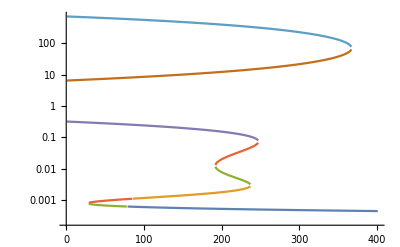

```mathematica
ListLogPlot[oneDT2,Joined->True]
```

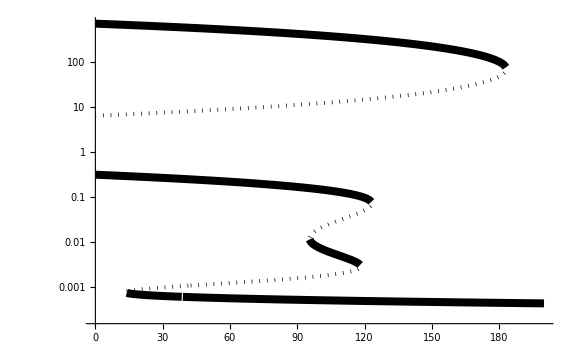

```mathematica
ListLogPlot[oneDT2,Joined->True,DataRange->{0,200},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]},ImageSize->Large]
```

#### Varying T_3

```mathematica
oneDT3=Transpose[Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->T3,Subscript[T, 4]->ss7Par13[[7]]},{Subscript[x, 1]}],{T3,0.1,130,0.1}]];
```

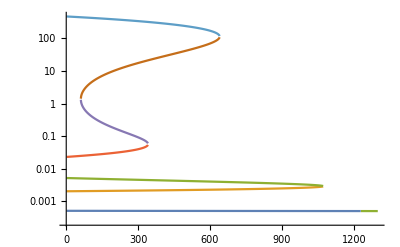

```mathematica
ListLogPlot[oneDT3,Joined->True]
```

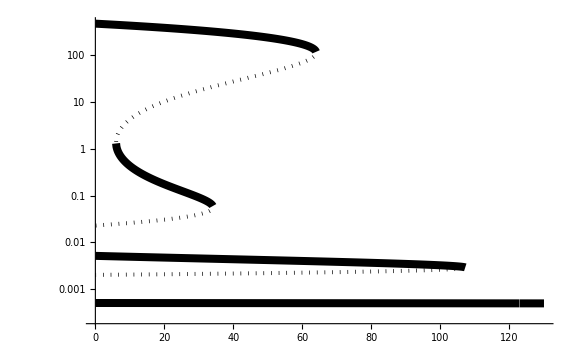

```mathematica
ListLogPlot[oneDT3,Joined->True,DataRange->{0,130},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]},ImageSize->Large]
```

#### Varying T_4

```mathematica
oneDT4=Transpose[Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->ss5Par3[[16]],Subscript[T, 4]->T4},{Subscript[x, 1]}],{T4,0,3,0.001}]];
```

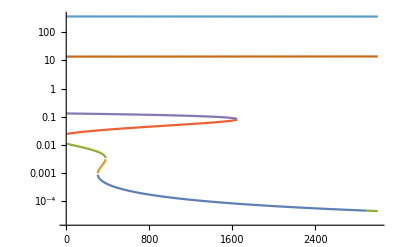

```mathematica
ListLogPlot[oneDT4,Joined->True]
```

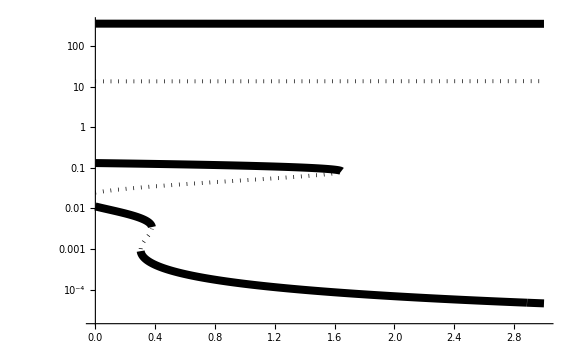

```mathematica
ListLogPlot[oneDT4,Joined->True,DataRange->{0,3},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.005]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]},ImageSize->Large]
```

#### Varying both T_2 and T_3

```mathematica
twoD=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[T, 4]->ss7Par13[[7]]},{Subscript[x, 1]}],{T2,0,300,2},{T3,0,150,1}];
```

```mathematica
logTransTwoD=Log10[Transpose[twoD,{2,3,1}]];dim=Dimensions[logTransTwoD];t3=Range[0,300,2];t2=Range[0,150,1];
nestedCoords=Table[{t2[[k]],t3[[j]],logTransTwoD[[i]][[j]][[k]]},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
coords=Table[Flatten[nestedCoords[[i]],1],{i,1,Length[nestedCoords]}];
```

```mathematica
normal3D=ListPointPlot3D[coords,PlotStyle->PointSize[Medium],ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ViewPoint->{1.9596537495237796,2.1803290214716005,1.6899474962572314},ViewVertical->{0.0684389894623006,0.08534421434061018,2.4849955606096703}]
```

-Graphics3D-

The options:

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,0.4},FaceGridsStyle→Automatic,ImageSize→Large,LabelStyle→{18,GrayLevel[0]},PlotRange→{{0.,150.},{0.,300.},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{1.95965,2.18033,1.68995},ViewVertical→{0.068439,0.0853442,2.485}}

#### Generating plots

```mathematica
normal3D=ListPointPlot3D[coords,PlotStyle->PointSize[Small],ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ViewPoint->{1.9596537495237796,2.1803290214716005,1.6899474962572314},ViewVertical->{0.0684389894623006,0.08534421434061018,2.4849955606096703}]
```

```mathematica
normal3D=ListPointPlot3D[coords,PlotStyle->PointSize[Small],ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ViewPoint->{-2.300292915262761,-1.9277515794653914,-1.5628263985038877},ViewVertical->{-0.13186973274698588,-0.0790653961217434,-2.470272045647693}]
```

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},PlotStyle->PointSize[Medium],PlotLegends->Automatic,ViewPoint->{1.9596537495237796,2.1803290214716005,1.6899474962572314},ViewVertical->{0.0684389894623006,0.08534421434061018,2.4849955606096703},ImageSize->Large]]
```

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},PlotStyle->PointSize[Small],PlotLegends->Automatic,ViewPoint->{1.9596537495237796,2.1803290214716005,1.6899474962572314},ViewVertical->{0.0684389894623006,0.08534421434061018,2.4849955606096703},ImageSize->Large]]
```

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},PlotStyle->PointSize[Small],PlotLegends->Automatic,ViewPoint->{-2.300292915262761,-1.9277515794653914,-1.5628263985038877},ViewVertical->{-0.13186973274698588,-0.0790653961217434,-2.470272045647693},ImageSize->Large]]
```